```mathematica
LayeredGraphPlot[ResourceFunction["MultiwaySystem"][{"Xo"->"oX","oX"->"Xo"},
"ooooooXoooooo",10,"EvolutionGraphStructure","IncludeStateWeights"->True,
VertexLabels->"VertexWeight"]]
```

-Graphics-

```mathematica
Length[Last[ResourceFunction["MultiwaySystem"][{"Xo"->"oX","oX"->"Xo"},
"ooooooXooooo",10,"AllStatesList","IncludeStepNumber"->True, 
"IncludeStateWeights"->True]]]
```

6

```mathematica
weights=Take[ResourceFunction["MultiwaySystem"][{"Xo"->"oX","oX"->"Xo"},
"ooooooXoooooo",10,"StateWeights","IncludeStateWeights"->True],-6]
```

{ooXoooooooooo→17/140,ooooXoooooooo→3/14,ooooooXoooooo→9/35,ooooooooXoooo→3/14,ooooooooooXoo→17/140,ooooooooooooX→1/28}

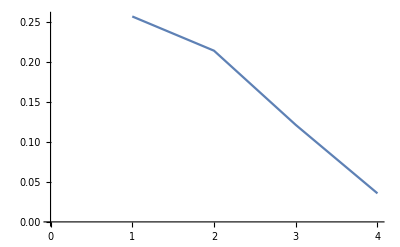

```mathematica
ListLinePlot[Last/@Take[weights,-4]]
```

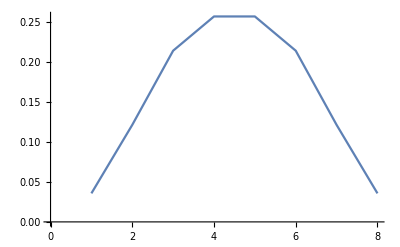

```mathematica
ListLinePlot[Last/@ Join[Reverse[Take[weights,-4]],Take[weights,-4]]]
```

Adding second photon propagating through the second slit.

```mathematica
LayeredGraphPlot[ResourceFunction["MultiwaySystem"][{"Xo"->"oX","oX"->"Xo"},"oooooooooXoooXooooooooo",6,"EvolutionGraphStructure"],AspectRatio->1/2]
```

-Graphics-

```mathematica
Length[Last[ResourceFunction["MultiwaySystem"][{"Xo"->"oX","oX"->"Xo"},"oooooooooXoooXooooooooo",6,"AllStatesList","IncludeStateWeights"->True,"IncludeStepNumber"->True]]]
```

35

```mathematica
weights = 
 Take[ResourceFunction["MultiwaySystem"][{"Xo" -> "oX", "oX" -> "Xo"},
    "oooooooooXoooXooooooooo", 6, "StateWeights", 
   "IncludeStateWeights" -> True], -18]
```

{ooooooooooXoXoooooooooo→5/64,ooooooooooXoooXoooooooo→75/896,oooooooooXoXooooooooooo→15/256,oooooooooXoooooXooooooo→225/3584,ooooooooXoXoooooooooooo→3/128,ooooooooXoooooooXoooooo→45/1792,oooooooXoXooooooooooooo→1/256,oooooooXoooooooooXooooo→15/3584,ooooooooooooXoXoooooooo→3/128,oooooooooooXoooXooooooo→15/448,ooooooooooXoooooXoooooo→45/1792,oooooooooXoooooooXooooo→9/896,ooooooooXoooooooooXoooo→3/1792,oooooooooooooXoXooooooo→1/256,ooooooooooooXoooXoooooo→5/896,oooooooooooXoooooXooooo→15/3584,ooooooooooXoooooooXoooo→3/1792,oooooooooXoooooooooXooo→1/3584}

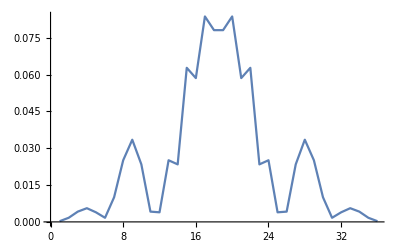

```mathematica
ListLinePlot[Last /@ Join[Reverse[weights], weights]]
```

```mathematica
ResourceFunction["MultiwaySystem"][{"S"->"X","S"->"Y","X"->"X","Y"->"Y"},"S",4,"EvolutionGraph"]
```

-Graphics-

```mathematica
ResourceFunction["TotalCausalInvariantQ"][{"S"->"X","S"->"Y","X"->"X","Y"->"Y"},4]
```

False

Two non intersecting branches can interact using Knuth-Bendix completion:

```mathematica
completion=ResourceFunction["CanonicalKnuthBendixCompletion"][{"S"->"X","S"->"Y","X"->"X","Y"->"Y"}]
```

{X→Y,Y→X}

The new evolution is then casual invariant:

```mathematica
ResourceFunction["MultiwaySystem"][Join[{"S"->"X","S"->"Y","X"->"X","Y"->"Y"},completion],"S",4,"EvolutionGraph"]
```

-Graphics-

```mathematica
ResourceFunction["TotalCausalInvariantQ"][Join[{"S"->"X","S"->"Y","X"->"X","Y"->"Y"},completion],4]
```

True

## Harmonic Oscillator

```mathematica
ResourceFunction["MultiwaySystem"][{"Xo"->"oX","oY"->"Yo","XO"->"YO","OY"->"OX"},#,10,"StatesGraph"]&/@{"OXoO","OXooO","OXoooO","OXooooO"}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ResourceFunction["MultiwaySystem"][{"Xo"->"oX","oY"->"Yo","XO"->"YO","OY"->"OX"},#,10,"EvolutionCausalGraphStructure"]&/@{"OXoO","OXooO","OXoooO","OXooooO"}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
LayeredGraphPlot[ResourceFunction["MultiwaySystem"][{"S"->"OXoO","S"->"OXooO","Xo"->"oX","oY"->"Yo","XO"->"YO","OY"->"OX"},"S",7,"StatesGraph"]]
```

-Graphics-

```mathematica
LayeredGraphPlot[ResourceFunction["MultiwaySystem"][{"S"->"A","S"->"E","A"->"B","B"->"C","C"->"D","D"->"A","E"->"F","F"->"G","G"->"H","H"->"I","I"->"J","J"->"E"},"S",7,"StatesGraph"]]
```

-Graphics-